## Mosquito population dynamics without IRS (only seasonality).

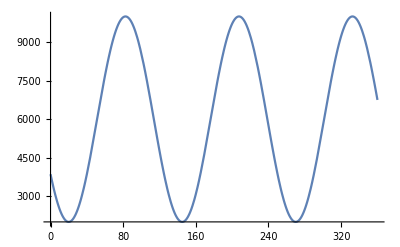

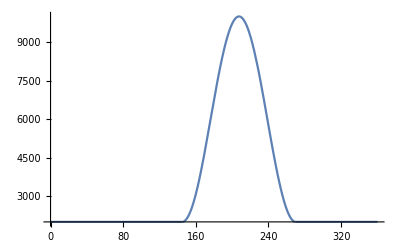

```mathematica
FirstDayOfRain=145; (* running day in a year of 360 days where each month is exactly 30 days. For example, 180 will be 30 of June *)
LastDayOfRain=270;(* running day in a year of 360 days where each month is exactly 30 days. For example, 180 will be 30 of June *)
Muliplier1=0.6;
Muliplier2=0.4;
BaseLine=2000;
phase=LastDayOfRain- FirstDayOfRain; (*This is the length of the rainy season*)
peakShift=phase*3/4-FirstDayOfRain ; (*This shifts the peak of the sin function towards where peak of rainy season should be.*)
K[t_]:=10000*(Muliplier1+Muliplier2*Sin[2π*(t/phase+peakShift/phase)]); (*Division by phase is to match the phase of the sin function to the seasonality; The value of the sin function is -1 to 1 so its multiplication by 0.5 and the addition of 0.5 is to define a minimum (positive) and a maximum value for the number of mosquitos. The 10000 is just an arbitrary number. *)
f[t_]:=Piecewise[{{K[Mod[t,360]],FirstDayOfRain<Mod[t,360]<LastDayOfRain}},BaseLine];  (*Seasonality in carrying capacity. In the rainy season, calculate K. Otherwise set to a baseline of 100 *)
Plot[K[t],{t,0,360}]
Plot[f[t],{t,0,360}]
```

```mathematica
(*MuE and MuL are the daily mortality of eggs+early larvae and of late larva stages,respectively.Both are density-dependent on the number of early and late larva stages,calculated as (A+L)/f,where f is the environmental carrying capacity at time t;\mu_E^0 and\mu_L^0 are assumed to be 0.035 and γ=13.25.These values are taken from Table 1 in White et al 2011. The equations are Eq.7 in the paper.*)
MuE[t_]:=0.035*(1+(A[t]+L[t])/f[t]); 
MuL[t_]:=0.035*(1+13.25*(A[t]+L[t])/f[t]);
```

```mathematica
(*Now solve the mosquito populatoin dynamics using the MuE and MuL.*)
TimeMax=720;
β=21.19; (* Average number of eggs laid per day; value from Table 1*)
de=6.64; (* length of developmental period of eggs+early larvae in days; the reciprocal of dE is the rate of progression to the next stage; value from Table 1*)
dl=3.72; (* length of developmental period of late larvae in days; Instars that survive development will become pupae at a rate given by the reciprocal of dL; value from Table 1*)
dp=0.64; (*  length of developmental period of pupae, in days; Value from Table 1 *)
(* When there is no IRS then the mortality rate of adults is just the basline MuM0. This goes in the calculation of M'[t] *)
MuM0=0.096; (* Daily mortality rate of adult mosquitos; value from Table 1*)
MuP=0.25; (* The pupae daily mortality rate; value ftom Table 1*)
system = {
A'[t] == β* M[t]-A[t]/de-MuE [t]A[t], (*Eggs and early larvae stages*)
L'[t]==A[t]/de-L[t]/dl-MuL[t]*L[t],(*late larvae stages*)
P'[t]==L[t]/dl-P[t]/dp-MuP*P[t], (*Pupae*)
M'[t]==0.5*P[t]/dp-MuM0*M[t], (* Adult mosquitos, half of them are female *)
(* Initial conditions *)
M[0]==10,
A[0]==100,
P[0]==500,
L[0]==200
};
sol = NDSolve[system,{A[t],L[t],P[t],M[t]},{t,0,TimeMax}];
```

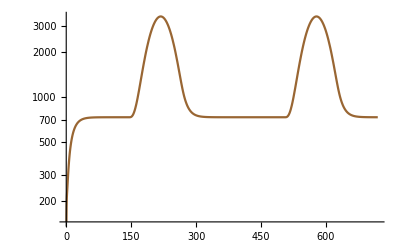

```mathematica
LogPlot[Evaluate[{M[t]}/.sol],{t,0,TimeMax}, PlotStyle->{Brown}] (* Plot abundance of adults *)
```

```mathematica
MosquitoNoIRS=Table[Evaluate[{M[t]}/.sol],{t,0,TimeMax}];
data=Transpose@{Range[0,TimeMax],Flatten[MosquitoNoIRS,2]};
data=Delete[data,1];
(*Export["~/Documents/malaria_interventions/mosquito_population_plosbiol_4.csv",data[[361;;720]]];*)
```

## IRS SCHEME OF GHANA FIELD DATA (Used For PLOS Biology)

```mathematica
(* The MuM function mimics the IRS applied in the field. IRS 1 had a coverage of 80%, IRS 2+3 had a coverage of 96%. To include the effect of the lifetime of the insecticides, and the fact that it takes time to spray all the compounds, we set the start time of the intervention to the middle time of the length it took to spray, and the total length of the intervention to the half-life of the insecticide. Specifically: 

IRS 1: Done between Oct-Dec 2013; We set starting date to Nov. 1st (running day 661). The intervention was with Organophosphates with lifetime of 2-3m. So we set the length to 75 days (661-735)
IRS 2: Done between May-Jul 2013; We set starting date to June 1st (running day 871). The intervention was with Organophosphates with lifetime of 2-3m. So we set the length to 75 days (871-945)
IRS 3: Done between Dec-Feb 2014; We set starting date to Jan 1st (running day 1081). The intervention was with 721+360 with lifetime of 4-6m. So we set the length to 150 days (1081-1230).

We let the model run for 5 years, to capture any effects of IRS on S5 and S6. We take the IRS data from day 661 because it takes one cycle (a year) to initiate the correct values (just like with the model without IRS, just seasonality) *)
w[c_,Q_,ϕ_,r_,ψ_]:=1-Q*c*ϕ*(1-(1-r)(1-ψ));
MuM [c1_,c2_,Q_,ϕ_,r_,ψ_,t_]:= Piecewise[{{-Log[0.91*w[c1,Q,ϕ,r,ψ]*0.74/1-Q *c1* ϕ* r*0.74]/3,301+360<=t<=375+360},{-Log[0.91*w[c2,Q,ϕ,r,ψ]*0.74/1-Q *c2* ϕ* r*0.74]/3,511+360<=t≤585+360||721+360<=t<=870+360}},MuM0];
```

```mathematica
Table[MuM[0.8,0.96,0.92,0.97,0.207,0.86,t],{t,1,1880}]
```

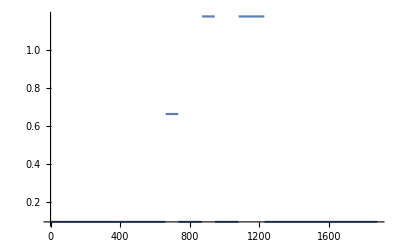

```mathematica
Plot[Evaluate[MuM[0.8,0.96,0.92,0.97,0.207,0.86,t]],{t,0,1880}]
```

```mathematica
TimeMax=5*360;
β=21.19; (* Average number of eggs laid per day; value from Table 1*)
de=6.64; (* length of developmental period of eggs+early larvae in days; the reciprocal of dE is the rate of progression to the next stage; value from Table 1*)
dl=3.72; (* length of developmental period of late larvae in days; Instars that survive development will become pupae at a rate given by the reciprocal of dL; value from Table 1*)
dp=0.64; (*  length of developmental period of pupae, in days; Value from Table 1 *)
MuM0=0.096; (* Daily mortality rate of adult mosquitos; value from Table 1*)
MuP=0.25; (* The pupae daily mortality rate; value ftom Table 1*)
system = {
A'[t] == β* M[t]-A[t]/de-MuE [t]A[t], (*Eggs and early larvae stages*)
L'[t]==A[t]/de-L[t]/dl-MuL[t]*L[t],(*late larvae stages*)
P'[t]==L[t]/dl-P[t]/dp-MuP*P[t], (*Pupae*)
M'[t]==0.5*P[t]/dp-MuM[0.8,0.96,0.92,0.97,0.207,0.86,t]*M[t], (* Adult mosquitos, half of them are female *)
(* Initial conditions *)
M[0]==10,
A[0]==100,
P[0]==500,
L[0]==200
};
sol = NDSolve[system,{A[t],L[t],P[t],M[t]},{t,0,TimeMax}];
```

```mathematica
LogPlot[Evaluate[{A[t],L[t],P[t],M[t]}/.sol],{t,0,TimeMax}, PlotStyle->{Blue,Red,Orange,Brown, Purple}] (* Plot abundance of all stages *)
```

1800

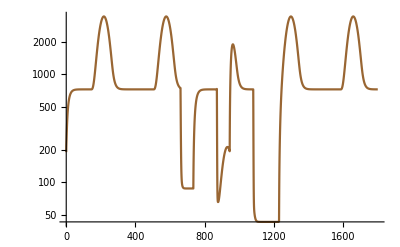

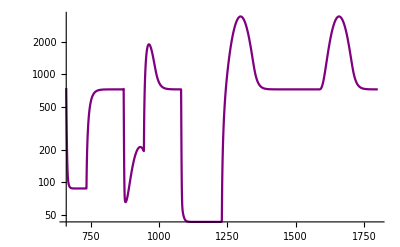

```mathematica
MosquitoIRS=Table[Evaluate[{M[t]}/.sol],{t,1,TimeMax}];
data=Transpose@{Range[1,TimeMax],Flatten[MosquitoIRS,2]};
Length[data]
LogPlot[Evaluate[{M[t]}/.sol],{t,1,TimeMax}, PlotStyle->{Brown}] (* Plot abundance of adults *)
(*data[[661;;TimeMax]]*)
LogPlot[Evaluate[{M[t]}/.sol],{t,661,TimeMax}, PlotStyle->{Purple}]
(*Export["~/Documents/malaria_interventions/IRS_Ghana.csv",data[[661;;TimeMax]]]*)
```